```mathematica
ClearAll["Global`*"]; 
u[x_]:=Cot[Sinh[2x]]; 

error[h_]:=Block[{},{
xi=0.4;c=0.2;
uvalueFD={u[xi-h],u[xi],u[xi+h]};
uvalueRFD5={u[xi-2h],u[xi-h],u[xi],u[xi+h],u[xi+2h]};
uvaluePM={u[xi-2h],u[xi-h],u[xi],u[xi+h],u[xi+2h]};
uvaluerbfhfd={u[xi-h],u[xi],u[xi+h],u''[xi-h],u''[xi+h]};
derivative=u''[xi];
(*FD2*)
setweights1={1/h^2,-2/h^2,1/h^2};
functionval1=setweights1.uvalueFD;
(*RBF-FD3*)
setweights2={9/(4 c^2)+1/h^2,-9/(2 c^2)-2/h^2,9/(4 c^2)+1/h^2};
functionval2=setweights2.uvalueFD;
(*RBF-FD5*)
setweights3={-185/(142 c^2)-1/(12 h^2),4/(3 h^2)+370/(71 c^2),-5/(2 h^2)-555/(71 c^2),4/(3 h^2)+370/(71 c^2),-185/(142 c^2)-1/(12 h^2)};
functionval3=setweights3.uvalueRFD5;
(*RBFHFDnew*)
setweights4={6/(5 h^2)+(3 (1575 c^2-892 h^2))/(21875 c^4),(6 (-1575/c^2-8750/h^2+(892 h^2)/c^4))/21875,6/(5 h^2)+(3 (1575 c^2-892 h^2))/(21875 c^4),-1/10-(27 h^2)/(250 c^2),-1/10-(27 h^2)/(250 c^2)};
functionval4=setweights4.uvaluerbfhfd;

Flatten@Abs@{derivative-functionval1,derivative-functionval2,derivative-functionval3,derivative-functionval4}
}][[1]]
```

6.53164-2.0047 x

9.76438-2.00483 x

15.3874-4.02192 x

12.1801-4.0019 x

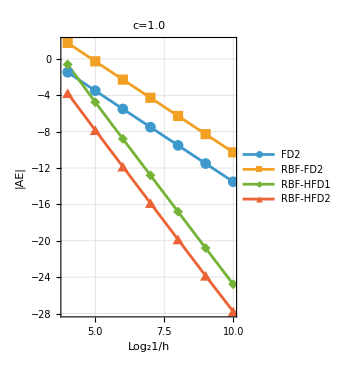

```mathematica
min=4;max=10;
error11=Log[2,N[Table[{1/j,error[j][[1]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit1=Fit[error11,{1,x},x]
error12=Log[2,N[Table[{1/j,error[j][[2]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit2=Fit[error12,{1,x},x]
error13=Log[2,N[Table[{1/j,error[j][[3]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit3=Fit[error13,{1,x},x]
error14=Log[2,N[Table[{1/j,error[j][[4]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit4=Fit[error14,{1,x},x]

ListPlot[{error11,error12,error13,error14},PlotRange->All,Joined->True,
PlotMarkers->Automatic,FrameLabel->{"Log_21/h","|AE|"},
PlotLabel->"c=1.0",
AspectRatio->1.5,(*PlotStyle->{Purple,Gray,Blue,Red},*)
PlotMarkers->{Automatic,Offset[2]},
PlotLegends->Placed[
{Style["FD2",9],
Style["RBF-FD2",9],
Style["RBF-HFD1",9],
Style["RBF-HFD2",9]
},
{Left,Bottom}],
PlotTheme->"Detailed",ImageSize->250
]
```

```mathematica
resul1=Transpose@{Flatten@Table[{j},{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[1]]],{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[2]]],{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[3]]],{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[4]]],{j,Table[1/2^h,{h,min,max}]}]
};
TableForm[resul1]
TeXForm[resul1]
```

1/16 | 3.60672×10^-1 | 6.97298×10^-1 | 1.087×10^-1 | 2.16999×10^-2
1/32 | 8.84423×10^-2 | 1.70937×10^-1 | 6.14923×10^-3 | 1.29304×10^-3
1/64 | 2.20052×10^-2 | 4.25276×10^-2 | 3.75241×10^-4 | 7.98682×10^-5
1/128 | 5.49476×10^-3 | 1.06191×10^-2 | 2.33141×10^-5 | 4.97713×10^-6
1/256 | 1.37328×10^-3 | 2.65397×10^-3 | 1.455×10^-6 | 3.10849×10^-7
1/512 | 3.43295×10^-4 | 6.63441×10^-4 | 9.09683×10^-8 | 1.9428×10^-8
1/1024 | 8.5822×10^-5 | 1.65857×10^-4 | 6.20707×10^-9 | 1.83964×10^-9

\left(
\begin{array}{ccccc}
 \frac{1}{16} & 3.60672\times 10^{-1} & 6.97298\times 10^{-1} & 1.087\times 10^{-1} & 2.16999\times 10^{-2} \\
 \frac{1}{32} & 8.84423\times 10^{-2} & 1.70937\times 10^{-1} & 6.14923\times 10^{-3} & 1.29304\times 10^{-3} \\
 \frac{1}{64} & 2.20052\times 10^{-2} & 4.25276\times 10^{-2} & 3.75241\times 10^{-4} & 7.98682\times 10^{-5} \\
 \frac{1}{128} & 5.49476\times 10^{-3} & 1.06191\times 10^{-2} & 2.33141\times 10^{-5} & 4.97713\times 10^{-6} \\
 \frac{1}{256} & 1.37328\times 10^{-3} & 2.65397\times 10^{-3} & 1.455\times 10^{-6} & 3.10849\times 10^{-7} \\
 \frac{1}{512} & 3.43295\times 10^{-4} & 6.63441\times 10^{-4} & 9.09683\times 10^{-8} & 1.9428\times 10^{-8} \\
 \frac{1}{1024} & 8.5822\times 10^{-5} & 1.65857\times 10^{-4} & 6.20707\times 10^{-9} & 1.83964\times 10^{-9} \\
\end{array}
\right)